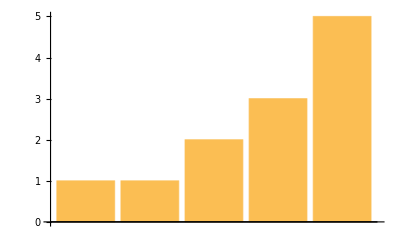

```mathematica
BarChart[{1,1,2,3,5}]
```

```mathematica
PieChart[Range[10]]
```

-Graphics-

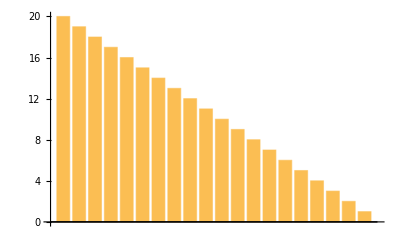

```mathematica
BarChart[Reverse[Range[20]]]
```

```mathematica
Column[Range[5]]
```

1
2
3
4
5

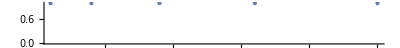

General::stop: Further output of Range::range will be suppressed during this calculation.

```mathematica
NumberLinePlot[{1,4,9,16,25}]
```

```mathematica
PieChart[{1,1,1,1,1,1,1,1,1,1}]
```

-Graphics-

```mathematica
Column[{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]}]
```

-Graphics-

```mathematica
{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
BarChart[Join[Range[10]],Reverse[Range[9]]]
```

BarChart::nonopt: Options expected (instead of {9,8,7,6,5,4,3,2,1}) beyond position 1 in BarChart[{1,2,3,4,5,6,7,8,9,10},{9,8,7,6,5,4,3,2,1}]. An option must be a rule or a list of rules.

```mathematica
BarChart[{1,2,3,4,5,6,7,8,9,10},{9,8,7,6,5,4,3,2,1}]
```

```mathematica
PieChart[1,2,3,4,5,6,7,8,9,10]
```

PieChart::nonopt: Options expected (instead of 10) beyond position 1 in PieChart[1,2,3,4,5,6,7,8,9,10]. An option must be a rule or a list of rules.

```mathematica
PieChart[Range[10]]
```

-Graphics-

```mathematica
{BarChart[Range[10]],LinePlot[Range[10]],PieChart[Range[10]]}
```

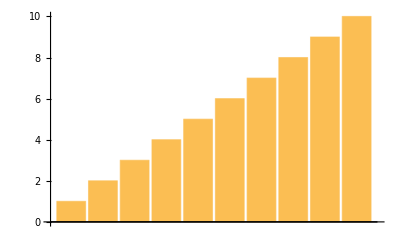
```mathematica
{-Graphics-,ListLinePlot[{1,2,3,4,5,6,7,8,9,10}],-Graphics-}
```

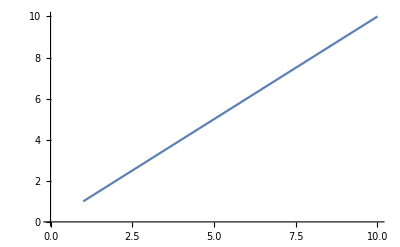
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
NumberLinePlot[1/2,1/3,1/9]
```

NumberLinePlot::nonopt: Options expected (instead of 1/9) beyond position 3 in NumberLinePlot[1/2,1/3,1/9]. An option must be a rule or a list of rules.

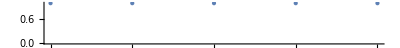
Column[-Graphics-,-Graphics-]

```mathematica
Column[NumberLinePlot[Range[5]],NumberLinePlot[Range[5]]]
```